```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

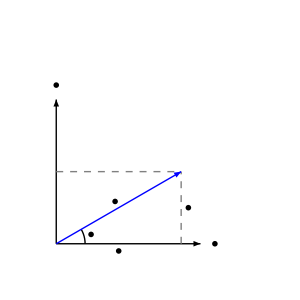

```mathematica
ClearAll[cheatSheatFig3,t,a,b,o,e1,e2,r,offset,offsetDistance,labelPosition,z]

t=Pi/6;
r=1;
a=r Cos[t];
b=r Sin[t];
z={a,b};
{e1,e2}=IdentityMatrix[2];
o=0 e1;
offsetDistance=0.05;
offset=offsetDistance*{-b,a};
labelPosition={a/2,b/2}+offset;

cheatSheatFig3=Graphics[{
Thick,
Black,
Arrow[{o,e1}],
Arrow[{o,e2}],
Text["\\mathrm{Re}"//MaTeX,1.1 e1],
Text["\\mathrm{Im}"//MaTeX,1.1 e2],

Circle[{0,0},0.2,{0,t}],
Text["\\theta"//MaTeX,{0.25 Cos[t/2],0.25 Sin[t/2]}],

Text["z"//MaTeX,labelPosition],
Text["a"//MaTeX,{a/2,0}-e2 offsetDistance],Text["b"//MaTeX,{a,b/2}+e1 offsetDistance],

{Dashed,Gray,Line[{{a,0},{a,b}}],Line[{{0,b},{a,b}}]},

Blue,
Arrow[{o,{a,b}}]
},

PlotRange->{{-0.2,1.5},{-0.2,1.5}},
AspectRatio->Automatic,
ImageSize->300
]
```

```mathematica
peeters`exportForLatex["cheatSheatFig3",cheatSheatFig3]
```

{cheatSheatFig3.eps,cheatSheatFig3pn.png}